```mathematica
Clear[w,h,f,g,x,y,s,weff];

SetAttributes[w, Constant];      (* EoS parameter of the barotropic fluid *)
SetAttributes[h, Constant];     (* roll parameter *)

f[x_,y_]=-(3/2) (2x+(w-1) x^3+x (w+1) (y^2-1)-Sqrt[2/3] h y^2);       (* x' *)
g[x_,y_]=-(3/2)  y ((w-1) x^2+(w+1) (y^2-1)+Sqrt[2/3] h x);                    (* y' *)
weff[x_,y_]=w+(1-w) x^2-(1+w) y^2;                                                   (* effective EoS parameter *)


s=Solve[{f[x,y]==0, g[x,y]==0}, {x,y}];
TableForm[s]                                                                                                                                            (* critical points *)
```

x→-1 | y→0
x→0 | y→0
x→1 | y→0
x→h/(√6) | y→-(√(6-h^2))/(√6)
x→h/(√6) | y→(√(6-h^2))/(√6)
x→(√(3/2) (1+w))/h | y→-(√(3/2) √(1-w^2))/h
x→(√(3/2) (1+w))/h | y→(√(3/2) √(1-w^2))/h

```mathematica
SetAttributes[w, Constant];      (* EoS parameter of the barotropic fluid *)
SetAttributes[h, Constant];     (* roll parameter *)


J={{-(3/2) (2+3 (x^2) (w-1)+(1+w) (y^2-1)), -(3/2) ((1+w) x 2 y-2 Sqrt[2/3] h y)},{ -(3/2)*y*((-1+w)*x*2+Sqrt[2/3]*h), -(3/2)*((w-1)*x^2+Sqrt[2/3]*h*x+(1+w)*(3*y^2-1))}};
MatrixForm[J]

v1={x->-1, y->0}
e1=Eigenvalues[J]/.v1;
e11:=Simplify[e1];
e11

v2={x->0 , y-> 0}
e2=Eigenvalues[J]/.v2;
e22:=Simplify[e2];
e22

v3={x->1 , y-> 0}
e3=Eigenvalues[J]/.v3;
e33:=Simplify[e3]
e33

v4={x->h/Sqrt[6] , y-> Sqrt[(6-h^2)/6]}
e4=Eigenvalues[J]/.v4;
e44:=Simplify[e4];
e44

v5={x->Sqrt[3/2]*((1+w)/h) , y-> Sqrt[(3*(1-w^2))/2]/h}
e5=Eigenvalues[J]/.v5;
e55:=Simplify[e5];
e55
```

(-3/2 (2+3 (-1+w) x^2+(1+w) (-1+y^2)) | -3/2 (-2 √(2/3) h y+2 (1+w) x y)
-3/2 (√(2/3) h+2 (-1+w) x) y | -3/2 (√(2/3) h x+(-1+w) x^2+(1+w) (-1+3 y^2)))

{x→-1,y→0}

{1/4 (12+√6 h-6 w-√(6 h^2+12 √6 h w+36 w^2)),1/4 (12+√6 h-6 w+√(6 h^2+12 √6 h w+36 w^2))}

{x→0,y→0}

{3/2 (-1+w),(3 (1+w))/2}

{x→1,y→0}

{1/4 (12-√6 h-6 w-√(6 h^2-12 √6 h w+36 w^2)),1/4 (12-√6 h-6 w+√(6 h^2-12 √6 h w+36 w^2))}

{x→h/(√6),y→(√(6-h^2))/(√6)}

{1/4 (-12+3 h^2-√((h^2-6 w)^2)-6 w),1/4 (-12+3 h^2+√((h^2-6 w)^2)-6 w)}

{x→(√(3/2) (1+w))/h,y→(√(3/2) √(1-w^2))/h}

{-3/4 (1-w+√(((-1+w) (-24 (1+w)^2+h^2 (7+9 w)))/h^2)),3/4 (-1+w+√(((-1+w) (-24 (1+w)^2+h^2 (7+9 w)))/h^2))}

```mathematica
(*  0<h^2<3(w+1)  *)

w=0;                    (* We consider matter domination *)
h=1;

a1=RegionPlot[weff[x,y]<-(1/3) && x^2+y^2<=1, {x, -1, 1}, {y,0 ,1},PlotStyle->RGBColor[1,0.85,0.69], BoundaryStyle->None];             (* region with accelerated expansion *)
a2=StreamPlot[{f[x,y], g[x,y]}, {x, -1,1}, {y,0,1},  PlotTheme->"Monochrome",RegionFunction->Function[{x,y}, x^2+y^2<=1 ], StreamPoints->Fine, StreamStyle->GrayLevel[0.85], PlotRange->All, Epilog->{RGBColor[0,0,0], PointSize[0.025], Point[{x,y}/.s]}, Frame->True, FrameStyle->Directive[Black,Thick], BaseStyle->{FontSize->15}, FrameLabel->{"x", Rotate["y", -Pi/2]}, AspectRatio->Automatic, ImageSize->Large];
t1={Text["A",{-0.99,0.06},BaseStyle->{FontSize->22,Bold,FontFamily->"Times",Italic}],Text["B",{0,0.06},BaseStyle->{FontSize->22,Bold,FontFamily->"Times",Italic}],Text["C",{0.99,0.06},BaseStyle->{FontSize->22,Bold,FontFamily->"Times",Italic}],Text["D", {Sqrt[1/6]+0.07,Sqrt[5/6]+0.02},BaseStyle->{FontSize->22,Bold,FontFamily->"Times",Italic}]};

Show[a1,a2,Graphics[t1], Epilog->{RGBColor[0,0,0], PointSize[0.025], Point[{x,y}/.s]}, Frame->True, FrameStyle->Directive[Black,Thick],FrameLabel->{Style[HoldForm[x],FontFamily->"Times",FontSize->22],
Style[HoldForm[Rotate["y", -Pi/2]],FontFamily->"Times",FontSize->22]}, AspectRatio->Automatic, ImageSize->Large,BaseStyle->{FontFamily->"Times",FontSize->16}]
```

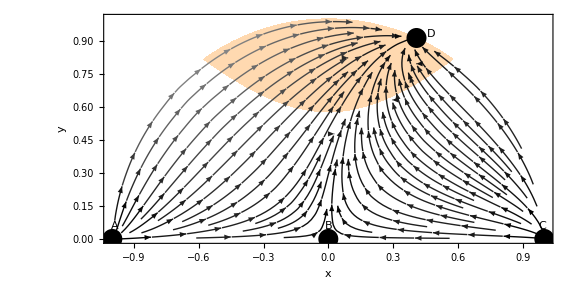

```mathematica
(*  3(w+1)<h^2<6 *)

w=0;                      (* We consider matter domination *)
h=2;

a3=StreamPlot[{f[x,y], g[x,y]}, {x, -1,1}, {y,0,1},  PlotTheme->"Monochrome",RegionFunction->Function[{x,y}, x^2+y^2<=1 ], StreamPoints->Fine, StreamStyle->GrayLevel[0.85], PlotRange->All, Epilog->{RGBColor[0,0,0], PointSize[0.025], Point[{x,y}/.s]}, Frame->True, FrameStyle->Directive[Black,Thick], BaseStyle->{FontSize->15}, FrameLabel->{"x", Rotate["y", -Pi/2]}, AspectRatio->Automatic, ImageSize->Large];
t2={Text["A",{-0.99,0.06},BaseStyle->{FontSize->22,Bold,FontFamily->"Times",Italic}],Text["B",{0,0.06},BaseStyle->{FontSize->22,Bold,FontFamily->"Times",Italic}],Text["C",{0.99,0.06},BaseStyle->{FontSize->22,Bold,FontFamily->"Times",Italic}],Text["D", {Sqrt[4/6]+0.07,Sqrt[2/6]+0.02},BaseStyle->{FontSize->22,Bold,FontFamily->"Times",Italic}],Text["E", {Sqrt[3/8]+0.07,Sqrt[3/8]+0.02},BaseStyle->{FontSize->22,Bold,FontFamily->"Times",Italic}]};

Show[a1,a3,Graphics[t2],Epilog->{RGBColor[0,0,0], PointSize[0.025], Point[{x,y}/.s]}, Frame->True, FrameStyle->Directive[Black,Thick], FrameLabel->{Style[HoldForm[x],FontFamily->"Times",FontSize->22],
Style[HoldForm[Rotate["y", -Pi/2]],FontFamily->"Times",FontSize->22]}, AspectRatio->Automatic, ImageSize->Large,BaseStyle->{FontFamily->"Times",FontSize->16}]
```

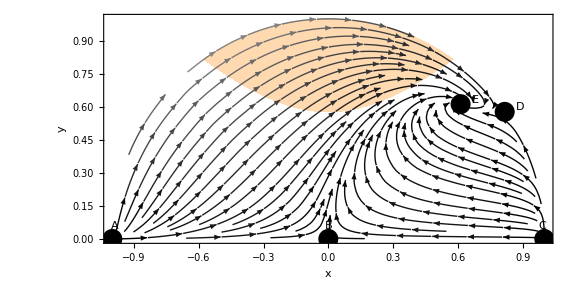

```mathematica
(*  h^2>6  *)

w=0;                    (* We consider matter domination *)
h=3;

s2={{x->1, y->0},{x->0, y->0}, {x->-1, y->0}, {x->Sqrt[3/2]*(1+w)/h, y->Sqrt[(3*(1-w^2))/(2*h^2)]}};

a4=StreamPlot[{f[x,y], g[x,y]}, {x, -1,1}, {y,0,1},  PlotTheme->"Monochrome",RegionFunction->Function[{x,y}, x^2+y^2<=1 ], StreamPoints->Fine, StreamStyle->GrayLevel[0.85], PlotRange->All, Epilog->{RGBColor[0,0,0], PointSize[0.025], Point[{x,y}/. s2]}, Frame->True, FrameStyle->Directive[Black,Thick], BaseStyle->{FontSize->15}, FrameLabel->{"x", Rotate["y", -Pi/2]}, AspectRatio->Automatic, ImageSize->Large];
t3={Text["A",{-0.99,0.06},BaseStyle->{FontSize->22,Bold,FontFamily->"Times",Italic}],Text["B",{0,0.06},BaseStyle->{FontSize->22,Bold,FontFamily->"Times",Italic}],Text["C",{0.99,0.06},BaseStyle->{FontSize->22,Bold,FontFamily->"Times",Italic}],Text["E", {Sqrt[1/6],Sqrt[1/6]+0.07},BaseStyle->{FontSize->22,Bold,FontFamily->"Times",Italic}]};


Show[a1, a4,Graphics[t3], Epilog->{RGBColor[0,0,0], PointSize[0.025], Point[{x,y}/. s2]}, Frame->True, FrameStyle->Directive[Black,Thick], FrameLabel->{Style[HoldForm[x],FontFamily->"Times",FontSize->22],
Style[HoldForm[Rotate["y", -Pi/2]],FontFamily->"Times",FontSize->22]}, AspectRatio->Automatic, ImageSize->Large,BaseStyle->{FontFamily->"Times",FontSize->16}]
```